{{1,3.},{2,6.09},{3,11.37},{4,18.5},{5,27.55},{6,41.55},{7,56.86},{8,75.81},{9,97.33},{10,119.03}}

{{1,3.},{2,4.52},{3,6.59},{4,11.47},{5,23.49},{6,30.33},{7,45.24},{8,69.4},{9,84.45},{10,96.05}}

{{1,2.94},{2,5.29},{3,9.3},{4,15.71},{5,27.9},{6,36.69},{7,49.96},{8,69.12},{9,102.02},{10,116.78}}

NBA line

FittedModel[-23.1847+11.0252 x]

0.922694

DBA line

FittedModel[-26.8393+12.8019 x]

0.911755

NBA parabola

FittedModel[-0.894671 x+1.09554 x^2]

0.995439

DBA parabola

FittedModel[-1.39166 x+1.31846 x^2]

0.996112

Fitted Equations

-0.224807 x+1.21245 x^2

-0.894671 x+1.09554 x^2

-1.39166 x+1.31846 x^2

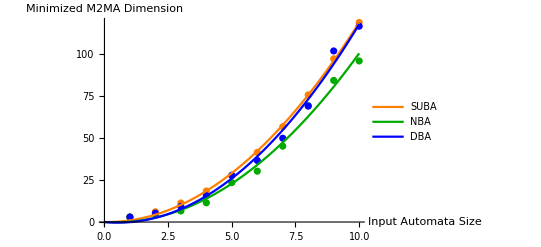

```mathematica
SUBAData = {{1, 3.00}, {2, 6.09}, {3, 11.37}, {4, 18.50}, {5, 27.55}, {6, 41.55}, {7, 56.86}, {8, 75.81}, {9, 97.33}, {10, 119.03}}

NBAData = {{1, 3.00}, {2, 4.52}, {3, 6.59}, {4, 11.47}, {5, 23.49}, {6, 30.33}, {7, 45.24}, {8, 69.40}, {9, 84.45}, {10, 96.05}}

DBAData = {{1, 2.94}, {2, 5.29}, {3, 9.30}, {4, 15.71}, {5, 27.9}, {6, 36.69}, {7, 49.96}, {8, 69.12}, {9, 102.02}, {10, 116.78}}

Print["NBA line"]
NBALineModel=LinearModelFit[NBAData,x,x]
NBALineModel["RSquared"]

Print["DBA line"]
DBALineModel=LinearModelFit[DBAData,x,x]
DBALineModel["RSquared"]

Print["NBA parabola"]
NBAQuadraticModel=NonlinearModelFit[NBAData,a*x^2+b*x,{a,b},x]
NBAQuadraticModel["RSquared"]

Print["DBA parabola"]
DBAQuadraticModel=NonlinearModelFit[DBAData,a*x^2+b*x,{a,b},x]
DBAQuadraticModel["RSquared"]

Print["Fitted Equations"]
SUBAParabola=Fit[SUBAData,{x, x^2},x]
NBAParabola=Fit[NBAData,{x, x^2},x]
DBAParabola = Fit[DBAData, {x, x^2}, x]

Show[ListPlot[SUBAData,PlotStyle->Orange], ListPlot[NBAData,PlotStyle->Darker[Green]],ListPlot[DBAData,PlotStyle->Blue], Plot[SUBAParabola,{x,0,10}, PlotStyle->Orange, PlotLegends->LineLegend[{"SUBA"}]],Plot[NBAParabola,{x,0,10}, PlotStyle->Darker[Green], PlotLegends->LineLegend[{"NBA"}]], Plot[DBAParabola,{x,0,10}, PlotStyle->Blue, PlotLegends->LineLegend[{"DBA"}]], AxesLabel-> {"Input Automata Size", "Minimized M2MA Dimension"}, ImageSize -> Scaled[.4]]
```